```mathematica
(*Homework #2 Problem 1*)
(*Solve the 1-d heat equation with conditions *)
(*u(0,t)=u(L,t)=0 and u(x,0)=f(x) and 0<x<L*)
(*f(x) = 180x(1-x)^2*)
Clear[a,b,f,L,k,t,myFSin,myFCos,mTplot,frames]

(*Here are our constants and function f[x]*)
f[x_]:=180x*(1-x)^2
L=1;
k=0.2;

(*Here is where we calculate the coefficients in the series expansion*)
b[n_]:=Integrate[f[x]*Sin[n*Pi*x/L],{x,0,L}]*(2/L)

Print["b[n]="]
Simplify[b[n],Assumptions->{n>0 && n ∈Integers}]

(*Here is the solution series to the heat equation*)
u[x_,t_,M_]:=Sum[b[n]*Sin[n*Pi*x/L]*E^(-k*(n*Pi/L)^2*t),{n,1,M}]

(*This is the solution to 10 terms in the series*)
myU[x_,t_]:=Evaluate[u[x,t,10]]

Print["u[x,t] to 10 terms:"]
myU[x,t]

(*Below is a plot that you can manipulate to see how the temperature
distribution decreases*)
Manipulate[Plot[myU[x,t],{x,0,L},PlotRange->{0,28}],{t,0,10}]

(*From the observing the graphs I can conclude that as t goes to infinity the heat
will be considerably dissipated*)
```

b[n]=

(720 (2+(-1)^n))/(n^3 π^3)

u[x,t] to 10 terms:

(720 ⅇ^(-1.97392 t) Sin[π x])/π^3+(270 ⅇ^(-7.89568 t) Sin[2 π x])/π^3+(80 ⅇ^(-17.7653 t) Sin[3 π x])/(3 π^3)+(135 ⅇ^(-31.5827 t) Sin[4 π x])/(4 π^3)+(144 ⅇ^(-49.348 t) Sin[5 π x])/(25 π^3)+(10 ⅇ^(-71.0612 t) Sin[6 π x])/π^3+(720 ⅇ^(-96.7221 t) Sin[7 π x])/(343 π^3)+(135 ⅇ^(-126.331 t) Sin[8 π x])/(32 π^3)+(80 ⅇ^(-159.888 t) Sin[9 π x])/(81 π^3)+(54 ⅇ^(-197.392 t) Sin[10 π x])/(25 π^3)

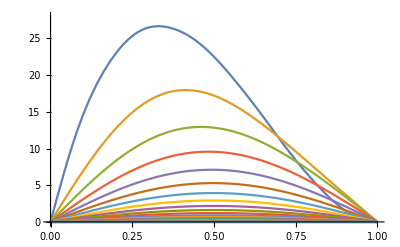

```mathematica
myPlotTable=Table[myU[x,t],{t,0,10,0.15}];
Plot[myPlotTable,{x,0,L},PlotRange->{0,28}]
(*Here you can see the individual time snapshots*)
(*Problem 1b: 
From the time snapshots t = 1,2,3,4,5.. the solution goes to zero, infact from the 3D plots as t->∞ ⟹ u(x,t)=0. This makes sense because the B.C. conditions suggest that at both ends the temperature is 0, therefore, the initial temperature will be forced temperature f(x)=u(x,0) that is initially given and that will slowly dissipate at t->∞*)
```

```mathematica
Clear[t]
(*Below is a 3d plot of the solution surface over time, notice the surface
flattens as time continues just as I concluded with the 2-d plots above*)
function = Evaluate[u[x,t,10]];
Plot3D[function,{x,0,L},{t,0,10},PlotRange->{0,27},ClippingStyle->None,BoxRatios->{1,1,1}]
```

-Graphics3D-

```mathematica
(*Problem 1c let f(x) = 2cos(3x) & L = Pi & k = 1*)
(*Repeat parts b) and c) again*)

Clear[a,b,f,L,k,t,myU,x]

(*Here are our constants and function f[x]*)
f[x_]:=2*Cos[3x]
L=Pi;
k=0.1;

(*Here is where we calculate the coefficients in the series expansion*)
b[n_]:=Integrate[f[x]*Sin[n*Pi*x/L],{x,0,L}]*(2/L)

Print["b[n]="]
Simplify[b[n],Assumptions->{n>0 && n ∈Integers}]

(*Here is the solution series to the heat equation*)
u[x_,t_,M_]:=Sum[b[n]*Sin[n*Pi*x/L]*E^(-k*(n*Pi/L)^2*t),{n,1,M}]

(*This is the solution to 10 terms in the series*)
myU[x_,t_]:=Evaluate[u[x,t,10]]

Print["u[x,t] to 10 terms:"]
myU[x,t]

(*Below is a plot that you can manipulate to see how the temperature
distribution decreases*)
Manipulate[Plot[myU[x,t],{x,0,L},PlotRange->{-2.2,2.2}],{t,0,10}]

(*From the observing the graphs I can conclude that as t goes to infinity the heat
will be considerably dissipated*)
```

b[n]=

(4 (1+(-1)^n) n)/((-9+n^2) π)

u[x,t] to 10 terms:

-(16 ⅇ^(-0.4 t) Sin[2 x])/(5 π)+(32 ⅇ^(-1.6 t) Sin[4 x])/(7 π)+(16 ⅇ^(-3.6 t) Sin[6 x])/(9 π)+(64 ⅇ^(-6.4 t) Sin[8 x])/(55 π)+(80 ⅇ^(-10. t) Sin[10 x])/(91 π)

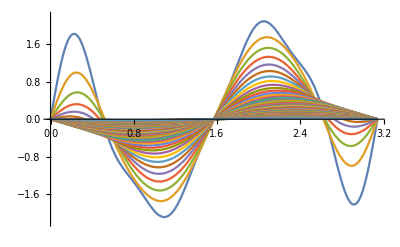

```mathematica
myPlotTable=Table[myU[x,t],{t,0,10,0.15}];
Plot[myPlotTable,{x,0,L},PlotRange->{-2.2,2.2}]

(*From the time snapshots t = 1,2,3,4,5.. the solution goes to zero, infact from the 3D plots as t->∞ ⟹ u(x,t)=0. This makes sense because the B.C. conditions suggest that at both ends the temperature is 0, therefore, the initial temperature will be forced temperature f(x)=u(x,0) that is initially given and that will slowly dissipate at t->∞*)
```

```mathematica
Clear[t]
(*Below is a 3d plot of the solution surface over time, notice the surface
flattens as time continues just as I concluded with the 2-d plots above*)
Plot3D[myU[x,t],{x,0,L},{t,0,10},PlotRange->{-2.2,2.2},ClippingStyle->None,BoxRatios->{1,1,1}]
```

-Graphics3D-